# Novel coronavirus (nCoV) phylodynamics

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/ncov-phylodynamics

## Options

### Functions

```mathematica
numericToCalendar[numDate_]:=DatePlus["2019-01-01",Quantity[numDate-2019,"Years"]]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

```mathematica
numberToString[num_]:=If[Negative[num],"-"<>StringDrop[ToString[num],1],ToString[num]]
```

```mathematica
Clear[frameTicks]
```

```mathematica
frameTicks[xMin_,xMax_,yMin_,yMax_,xTicksStep_,yTicksStep_]:={{Table[{i, numberToString[i], {0, 0.01}}, {i, Floor[yMin,yTicksStep], Ceiling[yMax,yTicksStep], yTicksStep}], None}, {Table[{i, numberToString[i], {0, 0.01}}, {i,Floor[xMin,xTicksStep], Ceiling[xMax,xTicksStep], xTicksStep}], None}}
```

```mathematica
frameTicks[]:={{None, None}, {Table[{i, If[EvenQ[i],numberToString[i],""], If[EvenQ[i],{0, 0.01},{0, 0.005}]}, {i,1994, 2014}], None}}
```

```mathematica
frameTicks[yMin_,yMax_,yTicksStep_]:={{Table[{i, numberToString[i], {0, 0.01}}, {i, Floor[yMin,yTicksStep], Ceiling[yMax,yTicksStep], yTicksStep}], None}, {Table[{i, If[EvenQ[i],numberToString[i],""], If[EvenQ[i],{0, 0.01},{0, 0.005}]}, {i,1994, 2014}], None}}
```

### Options

```mathematica
SetOptions[Plot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->400,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLinePlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->400,PlotRange->{0,All}];
```

```mathematica
SetOptions[RegionPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->400,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->400,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLogPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->400,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListContourPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->400];
```

```mathematica
SetOptions[ContourPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->400];
```

```mathematica
SetOptions[DiscretePlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->400,FrameStyle->Black,PlotRange->{0,All}];
```

```mathematica
SetOptions[Graphics,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->False,FrameTicksStyle->Black,ImageSize->400,FrameStyle->Black,PlotRange->{0,All}];
```

```mathematica
SetOptions[Histogram,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameTicksStyle->Black,FrameStyle->Black,ImageSize->400,PlotRange->{0,All},ChartBaseStyle->EdgeForm[Thin]];
```

```mathematica
SetOptions[SmoothDensityHistogram,FrameStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameTicksStyle->Black,FrameStyle->Black,ImageSize->400,PlotRange->{0,All}];
```

```mathematica
SetOptions[ArrayPlot,ImageSize->400,Frame->False,Mesh->True,MeshStyle->Thin];
```

## Exponential growth

With growth parameter

```mathematica
x0*ⅇ^(k t)
```

ⅇ^(k t) x0

```mathematica
x==ⅇ^(k t)/popSize
```

x==ⅇ^(k t)/popSize

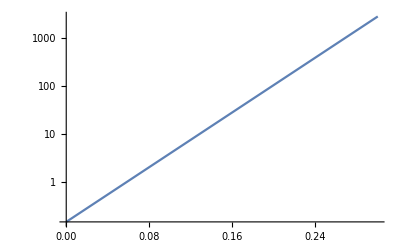

```mathematica
LogPlot[ⅇ^(33. t)/7,{t,0,0.3}]
```

With doubling time parameter

```mathematica
x0*2^(t/T)
```

2^(t/T) x0

```mathematica
growthRateInYearsToDoublingTimeInDays[growthRate_]:=365*Log[2]/growthRate
```

```mathematica
growthRateInYearsToDoublingTimeInDays[42.48]
```

5.95571

## Data

```mathematica
log=Import["ncov.log","Table"][[4;;-1]];
```

```mathematica
header=log[[1]]
```

{state,joint,prior,likelihood,treeModel.rootHeight,age(root),treeLength,exponential.popSize,exponential.growthRate,kappa,frequencies1,frequencies2,frequencies3,frequencies4,alpha,clock.rate,meanRate,treeLikelihood,branchRates,coalescent}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{state→1,joint→2,prior→3,likelihood→4,treeModel.rootHeight→5,age(root)→6,treeLength→7,exponential.popSize→8,exponential.growthRate→9,kappa→10,frequencies1→11,frequencies2→12,frequencies3→13,frequencies4→14,alpha→15,clock.rate→16,meanRate→17,treeLikelihood→18,branchRates→19,coalescent→20}

```mathematica
burnin=1000;
```

```mathematica
skip=3;
```

```mathematica
data=log[[burnin;;-1;;skip]];
```

```mathematica
length=Length[data]
```

1335

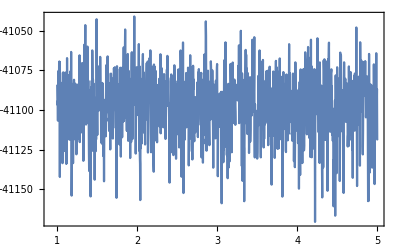

```mathematica
ListLinePlot[data[[All,{"state"/.headerRules,"joint"/.headerRules}]],PlotRange->All]
```

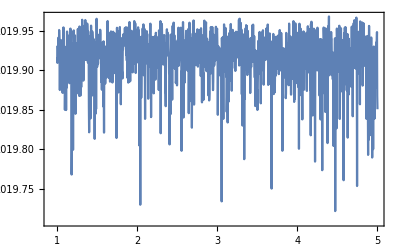

```mathematica
ListLinePlot[data[[All,{"state"/.headerRules,"age(root)"/.headerRules}]],PlotRange->All]
```

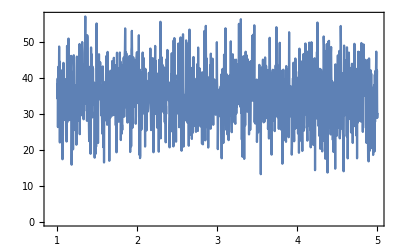

```mathematica
ListLinePlot[data[[All,{"state"/.headerRules,"exponential.growthRate"/.headerRules}]],PlotRange->All]
```

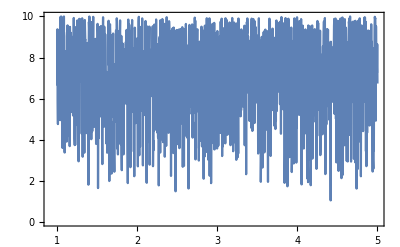

```mathematica
ListLinePlot[data[[All,{"state"/.headerRules,"exponential.popSize"/.headerRules}]],PlotRange->All]
```

## Growth rate

```mathematica
Median[data[[All,"exponential.growthRate"/.headerRules]]]
```

35.3551

```mathematica
Quantile[data[[All,"exponential.growthRate"/.headerRules]],0.025]
```

19.6108

```mathematica
Quantile[data[[All,"exponential.growthRate"/.headerRules]],0.975]
```

50.0146

```mathematica
growthRateInYearsToDoublingTimeInDays@Median[data[[All,"exponential.growthRate"/.headerRules]]]
```

7.15594

```mathematica
growthRateInYearsToDoublingTimeInDays@Quantile[data[[All,"exponential.growthRate"/.headerRules]],0.025]
```

12.901

```mathematica
growthRateInYearsToDoublingTimeInDays@Quantile[data[[All,"exponential.growthRate"/.headerRules]],0.975]
```

5.05849

## TMRCA and clock rate

```mathematica
numericToCalendar@Median[data[[All,"age(root)"/.headerRules]]]
```

Tue 3 Dec 2019 18:25:06

```mathematica
numericToCalendar@Quantile[data[[All,"age(root)"/.headerRules]],0.025]
```

Wed 30 Oct 2019 22:47:07

```mathematica
numericToCalendar@Quantile[data[[All,"age(root)"/.headerRules]],0.975]
```

Tue 17 Dec 2019 01:16:23

```mathematica
Median[data[[All,"clock.rate"/.headerRules]]]
```

0.000907725

```mathematica
Quantile[data[[All,"clock.rate"/.headerRules]],0.025]
```

0.000512803

```mathematica
Quantile[data[[All,"clock.rate"/.headerRules]],0.975]
```

0.00143243

## Single parameters

```mathematica
startDate=2019.805;endDate=2020.105;
```

```mathematica
Table[numericToCalendar[t],{t,startDate,endDate,tau}]
```

{Mon 21 Oct 2019 19:48:00,Tue 29 Oct 2019 03:00:00,Tue 5 Nov 2019 10:12:00,Tue 12 Nov 2019 17:24:00,Wed 20 Nov 2019 00:35:59,Wed 27 Nov 2019 07:47:59,Wed 4 Dec 2019 14:59:59,Wed 11 Dec 2019 22:12:00,Thu 19 Dec 2019 05:24:00,Thu 26 Dec 2019 12:36:00,Thu 2 Jan 2020 19:55:12,Fri 10 Jan 2020 03:36:00,Fri 17 Jan 2020 11:16:48,Fri 24 Jan 2020 18:57:36,Sat 1 Feb 2020 02:38:24,Sat 8 Feb 2020 10:19:12}

```mathematica
numericToCalendar[startDate]
```

Mon 21 Oct 2019 19:48:00

```mathematica
numericToCalendar[endDate]
```

Sat 8 Feb 2020 10:19:12

```mathematica
skylineNeTau[{tmrca_,popSize_,growthRate_}]:=Table[{t,ⅇ^(growthRate (t-tmrca))/popSize},{t,startDate,endDate,0.005}]
```

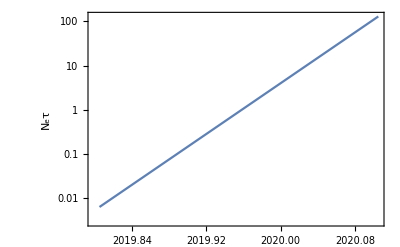

```mathematica
ListLogPlot[skylineNeTau[{2019.784,318.762,33.095}],Joined->True,FrameLabel->{"","N_eτ"}]
```

Assume a 7.5 day serial interval or a τ = 0.020 year serial interval.

If reported N_e τ is 2, it means that timescale of coalescence is 2 years. Divide by τ to get N_e.

```mathematica
tau=0.020;
```

Variance in offspring distribution required to get to population size N (prevalence). This is 2 for a standard epidemic compartmental model.

Variance σ^2 is R_0/ω+1. R0 is estimated to be 2.2. Omega is estimated to be 0.3.

```mathematica
meanR0=2.8;
```

```mathematica
varR0=meanR0^2/0.15+meanR0
```

55.0667

```mathematica
varR0/meanR0^2+1
```

8.02381

```mathematica
sigmaSquared[meanR0_,dispersion_]:=1/dispersion+1/meanR0+1
```

```mathematica
skylinePrev[{tmrca_,popSize_,growthRate_}]:=Module[{meanR0,k,σ2},
meanR0=RandomReal[{1.8,2.8}];
k=RandomReal[{0.15,0.30}];
σ2=sigmaSquared[meanR0,k];
Table[{t,σ2*ⅇ^(growthRate (t-tmrca))/(tau*popSize)},{t,startDate,endDate,0.005}]
]
```

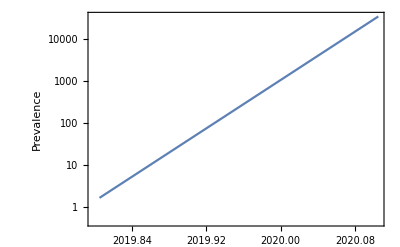

```mathematica
ListLogPlot[skylinePrev[{2019.784,318.762,33.095}],Joined->True,FrameLabel->{"","Prevalence"}]
```

## N_e τ and N_e Distributions

```mathematica
dateRangeToPlot={{2019,11,15},{2020,2,9}};
```

```mathematica
params[index_]:=data[[index,{"age(root)"/.headerRules,"exponential.popSize"/.headerRules,"exponential.growthRate"/.headerRules}]]
```

```mathematica
skylineNeTauList=Table[skylineNeTau[params[i]],{i,length}];
```

```mathematica
deltaT=0.004;
```

```mathematica
valuesAtTime[skylineList_,time_]:=Cases[Flatten[skylineList,1],{x_,y_}/;x≥time-deltaT&&x<time+deltaT][[All,2]]
```

```mathematica
quantileSkyline[skylineNeTau_,quantile_]:=Module[{skylineList},
skylineList=Table[skylineNeTau[params[i]],{i,length}];
Table[{numericToCalendar[t],Quantile[valuesAtTime[skylineList,t],quantile]},{t,startDate,endDate,0.005}]
]
```

```mathematica
medianNeTau=quantileSkyline[skylineNeTau,0.5];
```

```mathematica
lowerNeTau=quantileSkyline[skylineNeTau,0.025];
```

```mathematica
upperNeTau=quantileSkyline[skylineNeTau,0.975];
```

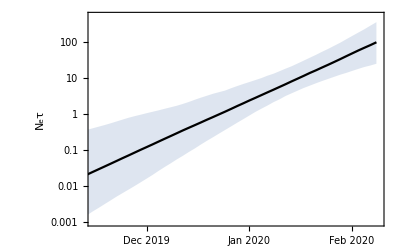

```mathematica
fig=DateListLogPlot[{lowerNeTau,medianNeTau,upperNeTau},Filling->1->{3},PlotStyle->{None,Black,None},PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"","N_eτ"},PlotRange->{dateRangeToPlot,{0.001,500}}]
```

```mathematica
Export["figures/netau.png",fig,"png",ImageResolution->300]
```

figures/netau.png

```mathematica
medianPrev=quantileSkyline[skylinePrev,0.5];
```

```mathematica
lowerPrev=quantileSkyline[skylinePrev,0.025];
```

```mathematica
upperPrev=quantileSkyline[skylinePrev,0.975];
```

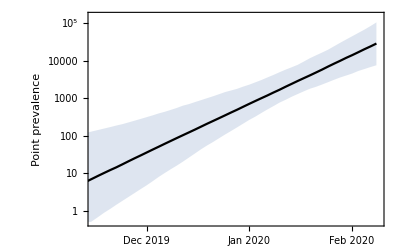

```mathematica
fig=DateListLogPlot[{lowerPrev,medianPrev,upperPrev},Filling->1->{3},PlotStyle->{None,Black,None},PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"","Point prevalence"},PlotRange->{dateRangeToPlot,{0.5,150000}}]
```

```mathematica
Export["figures/prevalence.png",fig,"png",ImageResolution->300]
```

figures/prevalence.png

```mathematica
Last[medianPrev]
```

{Sat 8 Feb 2020 10:19:12,28446.6}

```mathematica
Last[lowerPrev]
```

{Sat 8 Feb 2020 10:19:12,7491.59}

```mathematica
Last[upperPrev]
```

{Sat 8 Feb 2020 10:19:12,104327.}

## Total incidence

Each serial interval has a prevalence associated with it. Can discretize time into steps of serial interval, look at prevalence in each of these steps and add to the total.

```mathematica
quantileSkylineSerialInterval [skylineNeTau_,quantile_]:=Module[{skylineList,pairs},
skylineList=Table[skylineNeTau[params[i]],{i,length}];
pairs=Table[{numericToCalendar[t],Quantile[valuesAtTime[skylineList,t],quantile]},{t,startDate,endDate,tau}];
Transpose[{pairs[[All,1]],Accumulate[pairs[[All,2]]]}]
]
```

```mathematica
medianTotalIncidence=quantileSkylineSerialInterval[skylinePrev,0.5];
```

```mathematica
lowerTotalIncidence=quantileSkylineSerialInterval[skylinePrev,0.025];
```

```mathematica
upperTotalIncidence=quantileSkylineSerialInterval[skylinePrev,0.975];
```

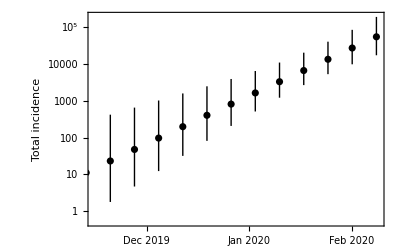

```mathematica
fig=DateListLogPlot[{lowerTotalIncidence,medianTotalIncidence,upperTotalIncidence},Filling->{1->{{3},Directive[Black]}},Joined->False,PlotStyle->{None,Black,None},PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"","Total incidence"},PlotRange->{dateRangeToPlot,{0.5,200000}}]
```

```mathematica
Export["figures/incidence.png",fig,"png",ImageResolution->300]
```

figures/incidence.png

```mathematica
Last[medianTotalIncidence]
```

{Sat 8 Feb 2020 10:19:12,55761.9}

```mathematica
Last[lowerTotalIncidence]
```

{Sat 8 Feb 2020 10:19:12,17500.5}

```mathematica
Last[upperTotalIncidence]
```

{Sat 8 Feb 2020 10:19:12,194395.}